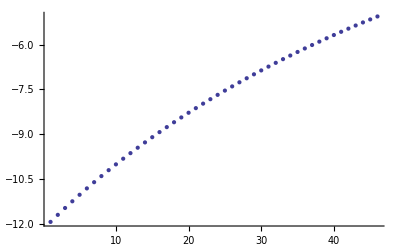

-11.9301
-11.6946
-11.4651
-11.2413
-11.023
-10.8099
-10.6019
-10.3987
-10.2002
-10.0062
-9.81646
-9.63091
-9.44936
-9.27168
-9.09774
-8.92741
-8.76057
-8.5971
-8.43691
-8.27988
-8.12591
-7.97492
-7.82681
-7.68151
-7.53892
-7.39897
-7.26159
-7.12671
-6.99425
-6.86415
-6.73636
-6.61081
-6.48744
-6.36619
-6.24702
-6.12988
-6.0147
-5.90146
-5.79009
-5.68056
-5.57283
-5.46685
-5.36258
-5.25998
-5.15903
-5.05967

5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50

ListPlot::nonopt: Options expected (instead of -11.9301
-11.6946
-11.4651
-11.2413
-11.023
-10.8099
-10.6019
-10.3987
-10.2002
-10.0062
« 36 ») beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50,-11.9301
-11.6946
-11.4651
-11.2413
-11.023
-10.8099
-10.6019
-10.3987
-10.2002
-10.0062
-9.81646
-9.63091
-9.44936
-9.27168
-9.09774
-8.92741
-8.76057
-8.5971
-8.43691
-8.27988
-8.12591
-7.97492
-7.82681
-7.68151
-7.53892
-7.39897
-7.26159
-7.12671
-6.99425
-6.86415
-6.73636
-6.61081
-6.48744
-6.36619
-6.24702
-6.12988
-6.0147
-5.90146
-5.79009
-5.68056
-5.57283
-5.46685
-5.36258
-5.25998
-5.15903
-5.05967]

```mathematica
aS=Table[i,{i,5,50,1}];
Sig=5.0;
Em1=80.0;
Ep0=8.85;
phi0=0.0258;
SigS=((Sig*aS)/(Em1*Ep0*phi0));
Za=1.0;
Fa=96500;
Na=0.1;
Qm=((Za*Fa*Na*aS*aS)/(Em1*Ep0*phi0))*10*^-6;
li=50;
ki=100;
Ba=100.0;
d=(aS/ki);
aLam=(aS/li);
Bs=(Ba/aS);
aZeta=SigS/(1+d);
Ep1=8.0;
akL=(d+aLam);
aOmegD1=1+aLam+((aLam*aLam)/(9*(1+2.0*Bs)));
aOmegD2=((aLam*aLam*Bs)/(9*(1+2.0*Bs)))*(3+aLam);
aOmegD=aOmegD1+aOmegD2;
aF1=(1.0/(1.0+2.0*Bs))+(Bs*(3+aLam)/(1.0+2.0*Bs));
aF2=(d*aLam/(d+aLam))+(d*Bs*(1+aLam)/(1.0+2.0*Bs));
aF31=3.0*d*d/(2.0*aLam*aLam);
aF32=aF1;
E5d=ExpIntegralE[5,d];
aF33=Exp[d]*E5d;
aF3=aF31*(1+aLam+(aLam*aLam*aF32)/3)*aF33;
aF41=(3.0*d*d*Exp[akL]/(2.0*aLam*aLam));
E5kL=ExpIntegralE[5,akL];
E4kL=ExpIntegralE[4,akL];
E3kL=ExpIntegralE[3,akL];
aF42=E5kL;
aF43=aLam*E4kL;
aF44=(aLam*aLam*E3kL)/3;
aF4=aF41*(aF42+aF43+aF44);
FactM=2.0*aZeta/(3.0*aOmegD);
aMob1=FactM*(aF1+aF2+aF3-aF4);


aCapK=1+d+(1.0/(1+d));
G11=Qm/(aLam*aLam*aOmegD);
G12=(aLam*aLam*Ep1)/(3*(Ep1+aCapK*Em1));
G13=aF1;
G1=G11*(1+aLam+G12*G13);
aMob2=-G1;

aMob=aMob1+aMob2;

ListPlot[aMob]
Data1=Column[Re[aMob]]
Data2=Column[aS]
ListPlot[Data2,Data1]
```

```mathematica
ListPlot[{{5.}, {6.95}, {8.9}, {10.85}, {12.8}, {14.75}, {16.7}, {18.65}, {20.6}, {22.55}, {24.5}, {26.45}, {28.4}, {30.349999999999998}, {32.3}, {34.25}, {36.2}, {38.15}, {40.1}, {42.05}, {44.}, {45.949999999999996}, {47.9}, {49.85}, {51.8}, {53.75}, {55.699999999999996}, {57.65}, {59.6}, {61.55}, {63.5}, {65.44999999999999}, {67.4}, {69.35}, {71.3}, {73.25}, {75.2}, {77.14999999999999}, {79.1}, {81.05}, {83.}, {84.95}, {86.89999999999999}, {88.85}, {90.8}, {92.75}, {94.7}, {96.64999999999999}, {98.6}, {100.55}, {102.5}, {104.45}, {106.39999999999999}, {108.35}, {110.3}, {112.25}, {114.2}, {116.14999999999999}, {118.1}, {120.05}, {122.}, {123.95}, {125.89999999999999}, {127.85}, {129.8}, {131.75}, {133.7}, {135.65}, {137.6}, {139.54999999999998}, {141.5}, {143.45}, {145.4}, {147.35}, {149.29999999999998}, {151.25}, {153.2}, {155.15}, {157.1}, {159.04999999999998}, {161.}, {162.95}, {164.9}, {166.85}, {168.79999999999998}, {170.75}, {172.7}, {174.65}, {176.6}, {178.54999999999998}, {180.5}, {182.45}, {184.4}, {186.35}, {188.29999999999998}, {190.25}, {192.2}, {194.15}, {196.1}, {198.04999999999998}, {200.}},{{-0.41479210317715154}, {0.2258301527300186}, {0.49863275428943765}, {0.6336151002226471}, {0.7044031159317738}, {0.7411884072424755}, {0.7584449887327211}, {0.7638846945539384}, {0.7619349175686612}, {0.7552797039012602}, {0.7456136222898493}, {0.734039764719013}, {0.7212929011763514}, {0.7078708017632572}, {0.6941146315368065}, {0.6802598043562341}, {0.6664690438776288}, {0.6528543806810208}, {0.6394920796261055}, {0.626432942169614}, {0.6137095205125014}, {0.6013412325590942}, {0.5893380273448247}, {0.5777030355489794}, {0.566434500627427}, {0.5555271944387855}, {0.5449734599268544}, {0.5347639816563876}, {0.5248883562846683}, {0.5153355149752743}, {0.5060940356771633}, {0.49715237303747145}, {0.4884990265149659}, {0.4801226619807826}, {0.47201219824590807}, {0.4641568671182789}, {0.45654625348821026}, {0.44917032037011395}, {0.4420194226497529}, {0.4350843123966905}, {0.4283561379275251}, {0.4218264382921308}, {0.4154871344631847}, {0.40933051820863275}, {0.4033492393954561}, {0.39753629229541027}, {0.39188500132540705}, {0.3863890065493775}, {0.3810422491858298}, {0.3758389573017929}, {0.3707736318245282}, {0.3658410329642937}, {0.36103616711210657}, {0.3563542742538433}, {0.3517908159247863}, {0.3473414637155421}, {0.3430020883304069}, {0.33876874919184374}, {0.33463768457934767}, {0.33060530228709073}, {0.3266681707820699}, {0.32282301084269843}, {0.3190666876567521}, {0.315396203357055}, {0.31180868997320305}, {0.30830140277782486}, {0.304871714006333}, {0.3015171069297083}, {0.2982351702605899}, {0.2950235928737294}, {0.29188015882272306}, {0.28880274263578964}, {0.28578930487423887}, {0.2828378879381483}, {0.2799466121046003}, {0.27711367178467855}, {0.2743373319861886}, {0.27161592496987264}, {0.26894784708758024}, {0.2663315557915743}, {0.2637655668048112}, {0.2612484514426407}, {0.25877883407698155}, {0.25635538973457006}, {0.2539768418214018}, {0.2516419599659889}, {0.2493495579744967}, {0.2470984918912749}, {0.24488765815869126}, {0.24271599187056123}, {0.24058246511381198}, {0.23848608539337288}, {0.23642589413556558}, {0.23440096526558818}, {0.23241040385493503}, {0.23045334483486646}, {0.2285289517722644}, {0.22663641570445134}, {0.22477495402974018}, {0.22294380945068232}, {0.22114224896717724}}]
```

ListPlot::nonopt: Options expected (instead of -0.414792
0.22583
0.498633
0.633615
0.704403
0.741188
0.758445
0.763885
0.761935
0.75528
« 91 ») beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[5.
6.95
8.9
10.85
12.8
14.75
16.7
18.65
20.6
22.55
24.5
26.45
28.4
30.35
32.3
34.25
36.2
38.15
40.1
42.05
44.
45.95
47.9
49.85
51.8
53.75
55.7
57.65
59.6
61.55
63.5
65.45
67.4
69.35
71.3
73.25
75.2
77.15
79.1
81.05
83.
84.95
86.9
88.85
90.8
92.75
94.7
96.65
98.6
100.55
102.5
104.45
106.4
108.35
110.3
112.25
114.2
116.15
118.1
120.05
122.
123.95
125.9
127.85
129.8
131.75
133.7
135.65
137.6
139.55
141.5
143.45
145.4
147.35
149.3
151.25
153.2
155.15
157.1
159.05
161.
162.95
164.9
166.85
168.8
170.75
172.7
174.65
176.6
178.55
180.5
182.45
184.4
186.35
188.3
190.25
192.2
194.15
196.1
198.05
200.,-0.414792
0.22583
0.498633
0.633615
0.704403
0.741188
0.758445
0.763885
0.761935
0.75528
0.745614
0.73404
0.721293
0.707871
0.694115
0.68026
0.666469
0.652854
0.639492
0.626433
0.61371
0.601341
0.589338
0.577703
0.566435
0.555527
0.544973
0.534764
0.524888
0.515336
0.506094
0.497152
0.488499
0.480123
0.472012
0.464157
0.456546
0.44917
0.442019
0.435084
0.428356
0.421826
0.415487
0.409331
0.403349
0.397536
0.391885
0.386389
0.381042
0.375839
0.370774
0.365841
0.361036
0.356354
0.351791
0.347341
0.343002
0.338769
0.334638
0.330605
0.326668
0.322823
0.319067
0.315396
0.311809
0.308301
0.304872
0.301517
0.298235
0.295024
0.29188
0.288803
0.285789
0.282838
0.279947
0.277114
0.274337
0.271616
0.268948
0.266332
0.263766
0.261248
0.258779
0.256355
0.253977
0.251642
0.24935
0.247098
0.244888
0.242716
0.240582
0.238486
0.236426
0.234401
0.23241
0.230453
0.228529
0.226636
0.224775
0.222944
0.221142]

```mathematica
ListPlot[{{5.}, {6.95}, {8.9}, {10.85}, {12.8}, {14.75}, {16.7}, {18.65}, {20.6}, {22.55}, {24.5}, {26.45}, {28.4}, {30.349999999999998}, {32.3}, {34.25}, {36.2}, {38.15}, {40.1}, {42.05}, {44.}, {45.949999999999996}, {47.9}, {49.85}, {51.8}, {53.75}, {55.699999999999996}, {57.65}, {59.6}, {61.55}, {63.5}, {65.44999999999999}, {67.4}, {69.35}, {71.3}, {73.25}, {75.2}, {77.14999999999999}, {79.1}, {81.05}, {83.}, {84.95}, {86.89999999999999}, {88.85}, {90.8}, {92.75}, {94.7}, {96.64999999999999}, {98.6}, {100.55}, {102.5}, {104.45}, {106.39999999999999}, {108.35}, {110.3}, {112.25}, {114.2}, {116.14999999999999}, {118.1}, {120.05}, {122.}, {123.95}, {125.89999999999999}, {127.85}, {129.8}, {131.75}, {133.7}, {135.65}, {137.6}, {139.54999999999998}, {141.5}, {143.45}, {145.4}, {147.35}, {149.29999999999998}, {151.25}, {153.2}, {155.15}, {157.1}, {159.04999999999998}, {161.}, {162.95}, {164.9}, {166.85}, {168.79999999999998}, {170.75}, {172.7}, {174.65}, {176.6}, {178.54999999999998}, {180.5}, {182.45}, {184.4}, {186.35}, {188.29999999999998}, {190.25}, {192.2}, {194.15}, {196.1}, {198.04999999999998}, {200.}},{{0.3773667529625738}, {0.4327161338949199}, {0.4639984345318133}, {0.4795713591040845}, {0.4848310543874409}, {0.48333362097938654}, {0.47745125927941284}, {0.4687791110413142}, {0.4583954296776911}, {0.44703108478393044}, {0.4351814699953166}, {0.42318118805308286}, {0.41125437244734564}, {0.3995488907127113}, {0.38815977972330135}, {0.3771454211055384}, {0.36653877920958533}, {0.35635525335081725}, {0.3465981903256414}, {0.3372627683726581}, {0.32833874008596886}, {0.3198123710898781}, {0.31166780889656565}, {0.3038880462399486}, {0.2964555947727195}, {0.2893529513534843}, {0.2825629155804902}, {0.27606880061402306}, {0.2698545675458094}, {0.26390490516803783}, {0.2582052709667528}, {0.25274190482081793}, {0.2475018237441635}, {0.242472803725362}, {0.237643353054065}, {0.23300268030737695}, {0.22854065927836226}, {0.2242477924756024}, {0.22011517434338204}, {0.2161344550005284}, {0.21229780503847637}, {0.2085978817311167}, {0.20502779687231215}, {0.2015810863582742}, {0.19825168156140155}, {0.1950338824923951}, {0.19192233271302264}, {0.18891199593878089}, {0.18599813425587627}, {0.18317628786817375}, {0.180442256285358}, {0.17779208086229303}, {0.17522202860049194}, {0.17272857712505943}, {0.1703084007539183}, {0.1679583575802027}, {0.16567547749314152}, {0.16345695106733302}, {0.16130011925492196}, {0.15920246381970724}, {0.1571615984565764}, {0.15517526054383868}, {0.1532413034799801}, {0.15135768956008372}, {0.14952248335063548}, {0.1477338455246735}, {0.14599002712224857}, {0.14428936420394542}, {0.14263027286778407}, {0.14101124460219205}, {0.13943084194992084}, {0.1378876944597844}, {0.1363804949049446}, {0.13490799574815895}, {0.1334690058359619}, {0.13206238730517758}, {0.13068705268646685}, {0.12934196219081526}, {0.12802612116596623}, {0.12673857771081473}, {0.1254784204367015}, {0.12424477636540122}, {0.12303680895437163}, {0.12185371624055434}, {0.12069472909466913}, {0.11955910957855308}, {0.11844614939864599}, {0.11735516844924024}, {0.11628551343957554}, {0.11523655659930031}, {0.11420769445720806}, {0.11319834668853561}, {0.11220795502643915}, {0.11123598223357747}, {0.11028191113002331}, {0.10934524367398189}, {0.10842550009204674}, {0.10752221805594366}, {0.10663495190293101}, {0.10576327189720379}, {0.10490676352984517}}]
```

ListPlot::nonopt: Options expected (instead of 0.377367
0.432716
0.463998
0.479571
0.484831
0.483334
0.477451
0.468779
0.458395
0.447031
« 91 ») beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[5.
6.95
8.9
10.85
12.8
14.75
16.7
18.65
20.6
22.55
24.5
26.45
28.4
30.35
32.3
34.25
36.2
38.15
40.1
42.05
44.
45.95
47.9
49.85
51.8
53.75
55.7
57.65
59.6
61.55
63.5
65.45
67.4
69.35
71.3
73.25
75.2
77.15
79.1
81.05
83.
84.95
86.9
88.85
90.8
92.75
94.7
96.65
98.6
100.55
102.5
104.45
106.4
108.35
110.3
112.25
114.2
116.15
118.1
120.05
122.
123.95
125.9
127.85
129.8
131.75
133.7
135.65
137.6
139.55
141.5
143.45
145.4
147.35
149.3
151.25
153.2
155.15
157.1
159.05
161.
162.95
164.9
166.85
168.8
170.75
172.7
174.65
176.6
178.55
180.5
182.45
184.4
186.35
188.3
190.25
192.2
194.15
196.1
198.05
200.,0.377367
0.432716
0.463998
0.479571
0.484831
0.483334
0.477451
0.468779
0.458395
0.447031
0.435181
0.423181
0.411254
0.399549
0.38816
0.377145
0.366539
0.356355
0.346598
0.337263
0.328339
0.319812
0.311668
0.303888
0.296456
0.289353
0.282563
0.276069
0.269855
0.263905
0.258205
0.252742
0.247502
0.242473
0.237643
0.233003
0.228541
0.224248
0.220115
0.216134
0.212298
0.208598
0.205028
0.201581
0.198252
0.195034
0.191922
0.188912
0.185998
0.183176
0.180442
0.177792
0.175222
0.172729
0.170308
0.167958
0.165675
0.163457
0.1613
0.159202
0.157162
0.155175
0.153241
0.151358
0.149522
0.147734
0.14599
0.144289
0.14263
0.141011
0.139431
0.137888
0.13638
0.134908
0.133469
0.132062
0.130687
0.129342
0.128026
0.126739
0.125478
0.124245
0.123037
0.121854
0.120695
0.119559
0.118446
0.117355
0.116286
0.115237
0.114208
0.113198
0.112208
0.111236
0.110282
0.109345
0.108426
0.107522
0.106635
0.105763
0.104907]

```mathematica
ListPlot[{{5.}, {6.95}, {8.9}, {10.85}, {12.8}, {14.75}, {16.7}, {18.65}, {20.6}, {22.55}, {24.5}, {26.45}, {28.4}, {30.349999999999998}, {32.3}, {34.25}, {36.2}, {38.15}, {40.1}, {42.05}, {44.}, {45.949999999999996}, {47.9}, {49.85}, {51.8}, {53.75}, {55.699999999999996}, {57.65}, {59.6}, {61.55}, {63.5}, {65.44999999999999}, {67.4}, {69.35}, {71.3}, {73.25}, {75.2}, {77.14999999999999}, {79.1}, {81.05}, {83.}, {84.95}, {86.89999999999999}, {88.85}, {90.8}, {92.75}, {94.7}, {96.64999999999999}, {98.6}, {100.55}, {102.5}, {104.45}, {106.39999999999999}, {108.35}, {110.3}, {112.25}, {114.2}, {116.14999999999999}, {118.1}, {120.05}, {122.}, {123.95}, {125.89999999999999}, {127.85}, {129.8}, {131.75}, {133.7}, {135.65}, {137.6}, {139.54999999999998}, {141.5}, {143.45}, {145.4}, {147.35}, {149.29999999999998}, {151.25}, {153.2}, {155.15}, {157.1}, {159.04999999999998}, {161.}, {162.95}, {164.9}, {166.85}, {168.79999999999998}, {170.75}, {172.7}, {174.65}, {176.6}, {178.54999999999998}, {180.5}, {182.45}, {184.4}, {186.35}, {188.29999999999998}, {190.25}, {192.2}, {194.15}, {196.1}, {198.04999999999998}, {200.}},{{0.3763640454593707}, {0.45583826821334145}, {0.5194152675295003}, {0.5719107346669676}, {0.6162868700262677}, {0.6544894437848593}, {0.6878585463929445}, {0.7173517620468917}, {0.7436741928401002}, {0.767358266189304}, {0.7888147812629237}, {0.8083666851471163}, {0.826272071426113}, {0.8427402320669035}, {0.857943106039315}, {0.8720236029109185}, {0.8851017592235851}, {0.8972793630436267}, {0.908643476866763}, {0.9192691560866886}, {0.9292215716133876}, {0.9385576850891174}, {0.9473275845982595}, {0.9555755589530702}, {0.9633409713235225}, {0.9706589711805567}, {0.9775610840382148}, {0.9840756997698321}, {0.9902284813545936}, {0.9960427071844089}, {1.001539562396708}, {1.0067383857297327}, {1.0116568807701913}, {1.0163112974574013}, {1.0207165887569154}, {1.0248865464952635}, {1.0288339196183733}, {1.0325705175545494}, {1.0361073008969302}, {1.0394544612444707}, {1.042621491735289}, {1.045617249558482}, {1.0484500115258475}, {1.051127523619213}, {1.0536570452884797}, {1.0560453891627943}, {1.0582989567390213}, {1.0604237705339452}, {1.0624255031165748}, {1.0643095033824073}, {1.066080820381644}, {1.0677442249728257}, {1.0693042295393371}, {1.0707651059752057}, {1.07213090212174}, {1.0734054568138038}, {1.0745924136775247}, {1.0756952338012844}, {1.076717207391603}, {1.077661464509824}, {1.078530984976947}, {1.079328607522904}, {1.080057038249668}, {1.080718858468949}, {1.0813165319709626}, {1.081852411771405}, {1.0823287463834643}, {1.0827476856531901}, {1.0831112861956491}, {1.0834215164636272}, {1.083680261478245}, {1.083889327249954}, {1.0840504449110375}, {1.0841652745862436}, {1.0842354090172712}, {1.0842623769613404}, {1.0842476463819484}, {1.0841926274447002}, {1.0840986753327972}, {1.083967092897033}, {1.083799133149241}, {1.0835960016113226}, {1.0833588585309681}, {1.0830888209701879}, {1.0827869647775705}, {1.0824543264527713}, {1.0820919049060864}, {1.0817006631256965}, {1.0812815297520268}, {1.0808354005732015}, {1.080363139937077}, {1.0798655820930303}, {1.0793435324633975}, {1.0787977688516073}, {1.0782290425867331}, {1.0776380796134313}, {1.0770255815266387}, {1.076392226554467}, {1.07573867049736}, {1.0750655476169049}, {1.0743734714846302}}]
```

ListPlot::nonopt: Options expected (instead of 0.376364
0.455838
0.519415
0.571911
0.616287
0.654489
0.687859
0.717352
0.743674
0.767358
« 91 ») beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[5.
6.95
8.9
10.85
12.8
14.75
16.7
18.65
20.6
22.55
24.5
26.45
28.4
30.35
32.3
34.25
36.2
38.15
40.1
42.05
44.
45.95
47.9
49.85
51.8
53.75
55.7
57.65
59.6
61.55
63.5
65.45
67.4
69.35
71.3
73.25
75.2
77.15
79.1
81.05
83.
84.95
86.9
88.85
90.8
92.75
94.7
96.65
98.6
100.55
102.5
104.45
106.4
108.35
110.3
112.25
114.2
116.15
118.1
120.05
122.
123.95
125.9
127.85
129.8
131.75
133.7
135.65
137.6
139.55
141.5
143.45
145.4
147.35
149.3
151.25
153.2
155.15
157.1
159.05
161.
162.95
164.9
166.85
168.8
170.75
172.7
174.65
176.6
178.55
180.5
182.45
184.4
186.35
188.3
190.25
192.2
194.15
196.1
198.05
200.,0.376364
0.455838
0.519415
0.571911
0.616287
0.654489
0.687859
0.717352
0.743674
0.767358
0.788815
0.808367
0.826272
0.84274
0.857943
0.872024
0.885102
0.897279
0.908643
0.919269
0.929222
0.938558
0.947328
0.955576
0.963341
0.970659
0.977561
0.984076
0.990228
0.996043
1.00154
1.00674
1.01166
1.01631
1.02072
1.02489
1.02883
1.03257
1.03611
1.03945
1.04262
1.04562
1.04845
1.05113
1.05366
1.05605
1.0583
1.06042
1.06243
1.06431
1.06608
1.06774
1.0693
1.07077
1.07213
1.07341
1.07459
1.0757
1.07672
1.07766
1.07853
1.07933
1.08006
1.08072
1.08132
1.08185
1.08233
1.08275
1.08311
1.08342
1.08368
1.08389
1.08405
1.08417
1.08424
1.08426
1.08425
1.08419
1.0841
1.08397
1.0838
1.0836
1.08336
1.08309
1.08279
1.08245
1.08209
1.0817
1.08128
1.08084
1.08036
1.07987
1.07934
1.0788
1.07823
1.07764
1.07703
1.07639
1.07574
1.07507
1.07437]

```mathematica
ListPlot[{{5.}, {6.95}, {8.9}, {10.85}, {12.8}, {14.75}, {16.7}, {18.65}, {20.6}, {22.55}, {24.5}, {26.45}, {28.4}, {30.349999999999998}, {32.3}, {34.25}, {36.2}, {38.15}, {40.1}, {42.05}, {44.}, {45.949999999999996}, {47.9}, {49.85}, {51.8}, {53.75}, {55.699999999999996}, {57.65}, {59.6}, {61.55}, {63.5}, {65.44999999999999}, {67.4}, {69.35}, {71.3}, {73.25}, {75.2}, {77.14999999999999}, {79.1}, {81.05}, {83.}, {84.95}, {86.89999999999999}, {88.85}, {90.8}, {92.75}, {94.7}, {96.64999999999999}, {98.6}, {100.55}, {102.5}, {104.45}, {106.39999999999999}, {108.35}, {110.3}, {112.25}, {114.2}, {116.14999999999999}, {118.1}, {120.05}, {122.}, {123.95}, {125.89999999999999}, {127.85}, {129.8}, {131.75}, {133.7}, {135.65}, {137.6}, {139.54999999999998}, {141.5}, {143.45}, {145.4}, {147.35}, {149.29999999999998}, {151.25}, {153.2}, {155.15}, {157.1}, {159.04999999999998}, {161.}, {162.95}, {164.9}, {166.85}, {168.79999999999998}, {170.75}, {172.7}, {174.65}, {176.6}, {178.54999999999998}, {180.5}, {182.45}, {184.4}, {186.35}, {188.29999999999998}, {190.25}, {192.2}, {194.15}, {196.1}, {198.04999999999998}, {200.}},{{0.036178870972232505}, {0.03322333342131366}, {0.030462683315768728}, {0.028022136528928984}, {0.025893293960404132}, {0.024037803191750567}, {0.02241451991808011}, {0.02098674356234444}, {0.019723577572040487}, {0.01859953852794964}, {0.01759372946723616}, {0.016689001593061414}, {0.015871227663246914}, {0.01512870752129176}, {0.014451693229685446}, {0.013832013214960373}, {0.013262775362346914}, {0.01273813204351316}, {0.012253093431701069}, {0.01180337843682605}, {0.011385295015093002}, {0.010995643504850855}, {0.010631638100307761}, {0.010290842689373506}, {0.009971118130943847}, {0.009670578694221518}, {0.009387555877492721}, {0.00912056820353611}, {0.008868295881635086}, {0.008629559453044097}, {0.008403301713476051}, {0.008188572344558755}, {0.007984514795134233}, {0.007790355039475193}, {0.007605391908047744}, {0.0074289887412539255}, {0.0072605661606049525}, {0.007099595787305815}, {0.006945594767029587}, {0.006798120983120562}, {0.006656768859640443}, {0.0065211656714306366}, {0.00639096829134673}, {0.006265860315569847}, {0.006145549516832721}, {0.006029765582838305}, {0.005918258103379017}, {0.00581079477489257}, {0.005707159795591452}, {0.005607152428022416}, {0.0055105857090629465}, {0.005417285290039161}, {0.005327088391930653}, {0.005239842862578411}, {0.005155406324479663}, {0.005073645403191342}, {0.004994435027596224}, {0.004917657794352484}, {0.004843203389772149}, {0.004770968063169561}, {0.004700854146418847}, {0.00463276961506422}, {0.004566627686853353}, {0.004502346454028381}, {0.00443984854611054}, {0.004379060820272152}, {0.004319914076701159}, {0.004262342796636516}, {0.0042062849009984705}, {0.004151681527750788}, {0.004098476826321159}, {0.0040466177675756495}, {0.003996053967993301}, {0.003946737526817294}, {0.0038986228750814865}, {0.003851666635514014}, {0.00380582749241446}, {0.0037610660706879164}, {0.003717344823292444}, {0.0036746279264257458}, {0.003632881181837346}, {0.0035920719257082237}, {0.003552168943588392}, {0.003513142390927973}, {0.003474963718778199}, {0.0034376056042731864}, {0.0034010418855388554}, {0.0033652475007024236}, {0.0033301984307055714}, {0.00329587164564655}, {0.0032622450544004936}, {0.00322929745728664}, {0.0031970085015688154}, {0.0031653586395955836}, {0.0031343290893959125}, {0.003103901797567532}, {0.0030740594043012926}, {0.0030447852104009375}, {0.003016063146165938}, {0.002987877742016494}, {0.0029602141007476672}}]
```

ListPlot::nonopt: Options expected (instead of 0.0361789
0.0332233
0.0304627
0.0280221
0.0258933
0.0240378
0.0224145
0.0209867
0.0197236
0.0185995
« 91 ») beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[5.
6.95
8.9
10.85
12.8
14.75
16.7
18.65
20.6
22.55
24.5
26.45
28.4
30.35
32.3
34.25
36.2
38.15
40.1
42.05
44.
45.95
47.9
49.85
51.8
53.75
55.7
57.65
59.6
61.55
63.5
65.45
67.4
69.35
71.3
73.25
75.2
77.15
79.1
81.05
83.
84.95
86.9
88.85
90.8
92.75
94.7
96.65
98.6
100.55
102.5
104.45
106.4
108.35
110.3
112.25
114.2
116.15
118.1
120.05
122.
123.95
125.9
127.85
129.8
131.75
133.7
135.65
137.6
139.55
141.5
143.45
145.4
147.35
149.3
151.25
153.2
155.15
157.1
159.05
161.
162.95
164.9
166.85
168.8
170.75
172.7
174.65
176.6
178.55
180.5
182.45
184.4
186.35
188.3
190.25
192.2
194.15
196.1
198.05
200.,0.0361789
0.0332233
0.0304627
0.0280221
0.0258933
0.0240378
0.0224145
0.0209867
0.0197236
0.0185995
0.0175937
0.016689
0.0158712
0.0151287
0.0144517
0.013832
0.0132628
0.0127381
0.0122531
0.0118034
0.0113853
0.0109956
0.0106316
0.0102908
0.00997112
0.00967058
0.00938756
0.00912057
0.0088683
0.00862956
0.0084033
0.00818857
0.00798451
0.00779036
0.00760539
0.00742899
0.00726057
0.0070996
0.00694559
0.00679812
0.00665677
0.00652117
0.00639097
0.00626586
0.00614555
0.00602977
0.00591826
0.00581079
0.00570716
0.00560715
0.00551059
0.00541729
0.00532709
0.00523984
0.00515541
0.00507365
0.00499444
0.00491766
0.0048432
0.00477097
0.00470085
0.00463277
0.00456663
0.00450235
0.00443985
0.00437906
0.00431991
0.00426234
0.00420628
0.00415168
0.00409848
0.00404662
0.00399605
0.00394674
0.00389862
0.00385167
0.00380583
0.00376107
0.00371734
0.00367463
0.00363288
0.00359207
0.00355217
0.00351314
0.00347496
0.00343761
0.00340104
0.00336525
0.0033302
0.00329587
0.00326225
0.0032293
0.00319701
0.00316536
0.00313433
0.0031039
0.00307406
0.00304479
0.00301606
0.00298788
0.00296021]

```mathematica
ListPlot[{{0.1}, {0.19}, {0.28}, {0.37}, {0.45999999999999996}, {0.5499999999999999}, {0.64}, {0.73}, {0.82}, {0.9099999999999999}, {0.9999999999999999}},{{0.7977856242240986}, {0.8737631896577656}, {0.9322074700857392}, {0.9785598301335284}, {1.0162211223774846}, {1.0474261928735116}, {1.0737041468939457}, {1.0961365465956938}, {1.1155099826145838}, {1.1324102139956218}, {1.147282417551778}}]
```

ListPlot::nonopt: Options expected (instead of 0.797786
0.873763
0.932207
0.97856
1.01622
1.04743
1.0737
1.09614
1.11551
1.13241
« 1 ») beyond position 1 in ListPlot[TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[0.1
0.19
0.28
0.37
0.46
0.55
0.64
0.73
0.82
0.91
1.,0.797786
0.873763
0.932207
0.97856
1.01622
1.04743
1.0737
1.09614
1.11551
1.13241
1.14728]

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

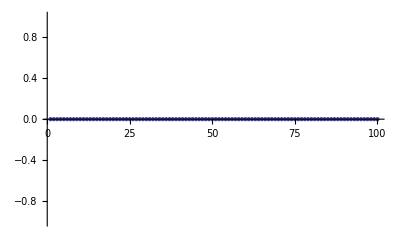

0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.

1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94
95
96
97
98
99
100

ListPlot::nonopt: Options expected (instead of 0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
« 50 ») beyond position 3 in TagBox[GridBox[{{. An option must be a rule or a list of rules.

ListPlot[1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94
95
96
97
98
99
100,0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.]

```mathematica
ListPlot[{{1.}, {1.9}, {2.8}, {3.7}, {4.6}, {5.5}, {6.4}, {7.3}, {8.2}, {9.1}, {10.}},]
```